```mathematica
imgsize=900;
```

```mathematica
NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../neupackage/mma/neumat.wl"]
```

## Akhmedov’s Parametric Resonance

For a castle wall matter profile

```mathematica
?Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.

```mathematica
lada[lambda1_,lambda2_,t1_,t2_,x_]:=Piecewise[{{lambda1,0≤Mod[x,t1+t2]<=t1},{lambda2,t1<Mod[x,t1+t2]<(t1+t2)}}]
```

Test this profile

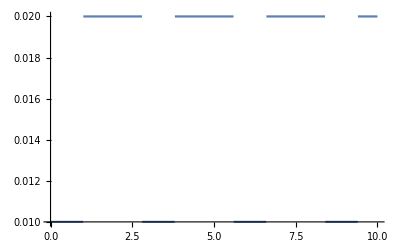

```mathematica
Plot[lada[0.01,0.02,1,1.8,x],{x,0,10}]
```

For a matter profile with two periodic densities λ_1([0,T1]) and λ_2 ([T1,T1+T2]), fourier series of it is
λ(x)=∑_n Λ_n e^(i ω_0 n x)
where the coefficients are calculated using

```mathematica
ladaCoeff[lambda1_,lambda2_,t1_,t2_,n_]:=I/(2π n)( -lambda1+(lambda1-lambda2)Exp[-I (2π)/(t1+t2)n t1]+lambda2 Exp[-I 2π n] )
```

Notice that n=0 should be dealt with independently (Λ_0=0)

```mathematica
ladaCoeff0[lambda1_,lambda2_,t1_,t2_]:=(lambda1 t1+lambda2 t2)/(t1+t2)
```

```mathematica
ladaCoeff[0.01,0.02,1,1.8,1]
```

-0.00124432+0.00258386 ⅈ

We notice that the coefficient will decrease as n increases, so that the modes becomes less important as n becomes very large.

Reconstruct the matter profile using Fourier series (approximately)

```mathematica
ladaRecon[lambda1_,lambda2_,t1_,t2_,n_,x_]:=Total@Table[ladaCoeff[lambda1,lambda2,t1,t2,nTab]Exp[I 2π nTab x/(t1+t2)],{nTab,n}]
```

```mathematica
ladaRecon[0.01,0.02,1,1.8,Table[i,{i,1,4}],x]
```

(-0.00124432+0.00258386 ⅈ) ⅇ^((0.+2.24399 ⅈ) x)+(0.000775823+0.000972851 ⅈ) ⅇ^((0.+4.48799 ⅈ) x)-(0.000230182-0.0000525376 ⅈ) ⅇ^((0.+6.73198 ⅈ) x)-(0.000172637-0.000756371 ⅈ) ⅇ^((0.+8.97598 ⅈ) x)

```mathematica
ladaReconExampleLow[x_]:=Re@ladaRecon[0.01,0.02,1,1.8,Table[i,{i,1,3}],x]+ladaCoeff0[0.01,0.02,1,1.8]+Re@ladaRecon[0.01,0.02,1,1.8,-Table[i,{i,1,3}],x]

ladaReconExample[x_]:=Re@ladaRecon[0.01,0.02,1,1.8,Table[i,{i,1,10}],x]+ladaCoeff0[0.01,0.02,1,1.8]+Re@ladaRecon[0.01,0.02,1,1.8,-Table[i,{i,1,10}],x]
```

```mathematica
ladaReconExampleLowListData=Table[{x,ladaReconExampleLow[x]},{x,0,10,0.01}];
ladaReconExampleListData=Table[{x,ladaReconExample[x]},{x,0,10,0.01}];
ladaExampleListData=Table[{x,lada[0.01,0.02,1,1.8,x]},{x,0,10,0.01}];
```

```mathematica
reconPlot=ListPlot[{ladaExampleListData,ladaReconExampleLowListData,ladaReconExampleListData},Joined->{True,True,True},Frame->True,ImageSize->imgsize,PlotLabel->"Fourier Series of Castle Wall Profile",FrameLabel->{"ω_mx","Perturbation Amplitude/ω_m"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},PlotMarkers->{" ","  ","   "},PlotStyle->{Black,Directive[Darker@Blue,DotDashed],Directive[Darker@Red,Dotted],Red},ImagePadding->{{Automatic, 10}, {Automatic, 10}},PlotLegends->Placed[{"Castle Wall Profile","Reconstruction Using Modes -3 to 3","Reconstruction Using Modes -10 to 10"},Below]]
```

-Graphics-

```mathematica
(*Export["../ipynb/papers/assets/parametric-resonance/reconstruction-of-castle-wall-0point01-0point02-1-1point8.pdf",reconPlot]
Export["../ipynb/papers/assets/parametric-resonance/reconstruction-of-castle-wall-0point01-0point02-1-1point8.png",reconPlot]*)
```

## Even Profile

```mathematica
ladaEven[lambda1_,lambda2_,t1_,t2_,x_]:=Piecewise[{{lambda1,0≤Mod[x,t1+t2]<=t1/2},{lambda2,t1/2<Mod[x,t1+t2]<=(t1/2+t2)},{lambda1,t1/2+t2<Mod[x,t1+t2]<(t1+t2)}}]
```

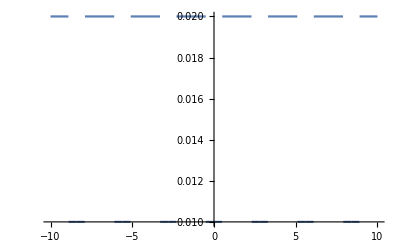

```mathematica
Plot[ladaEven[0.01,0.02,1,1.8,x],{x,-10,10}]
```

```mathematica
ladaEvenCoeff[lambda1_,lambda2_,t1_,t2_,n_]:=2/(π n)( lambda2 (Sin[n Pi]-Sin[n Pi t1/(t1+t2)])+lambda1 Sin[n Pi t1/(t1+t2)] )
```

```mathematica
ladaknEven[lambda1_,lambda2_,t1_,t2_,n_]:=n 2 Pi/(t1+t2)
```

```mathematica
ladaEvenCoeff0[lambda1_,lambda2_,t1_,t2_]:=2(lambda1 t1+lambda2 t2)/(t1+t2)
```

```mathematica
ladaEvenRecon[lambda1_,lambda2_,t1_,t2_,n_,x_]:=Total@Table[ladaEvenCoeff[lambda1,lambda2,t1,t2,nTab]Cos[2π nTab x/(t1+t2)],{nTab,n}]
```

```mathematica
ladaEvenReconExample[x_]:=Re@ladaEvenRecon[0.01,0.02,1,1.8,Table[i,{i,1,10}],x]+ladaEvenCoeff0[0.01,0.02,1,1.8]/2
ladaEvenReconExampleListData=Table[{x,ladaEvenReconExample[x]},{x,0,10,0.01}];

ladaEvenReconExampleLow[x_]:=Re@ladaEvenRecon[0.01,0.02,1,1.8,Table[i,{i,1,3}],x]+ladaEvenCoeff0[0.01,0.02,1,1.8]/2
ladaEvenReconExampleLowListData=Table[{x,ladaEvenReconExampleLow[x]},{x,0,10,0.01}];
```

```mathematica
ladaEvenExampleListData=Table[{x,ladaEven[0.01,0.02,1,1.8,x]},{x,0,10,0.01}];
```

```mathematica
reconEvenPlot=ListPlot[{ladaEvenExampleListData[[;;;;1]],ladaEvenReconExampleLowListData,ladaEvenReconExampleListData},Joined->{True,True,True},Frame->True,ImageSize->imgsize,PlotLabel->"Fourier Series of Castle Wall Profile",FrameLabel->{"ω_mx","Perturbation Amplitude/ω_m"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},PlotMarkers->{" ","  ","   "},PlotStyle->{Black,Directive[Darker@Blue,DotDashed],Directive[Darker@Red,Dotted],Red},ImagePadding->{{Automatic, 10}, {Automatic, 10}},PlotLegends->Placed[{"Castle Wall Profile","Reconstruction Using Modes 0 to 3","Reconstruction Using Modes 0 to 10"},Below]]
```

-Graphics-

```mathematica
(*Export["../ipynb/papers/assets/parametric-resonance/reconstruction-of-even-castle-wall-0point01-0point02-1-1point8.pdf",reconEvenPlot]
Export["../ipynb/papers/assets/parametric-resonance/reconstruction-of-even-castle-wall-0point01-0point02-1-1point8.png",reconEvenPlot]*)
```

Numerical Result

We construct a system with the following parameters
n q 2π/X = ω_m
λ_m=0.5 λ_MSW (this is specified to fix θ_m)

On the other hand, we require
Λ_0 as the background density, so that the Hamiltonian, in units of ω_m is
H = -1/2 σ_3+1/2 δλ cos 2 θ_m σ_3-1/2 δλ sin 2 θ_m σ_1
where δλ is in unit of ω_m

Let’s simplify the problem and use equal period of the two densities, X_1=X_2=X_0=X/2. The requirements are
1. Resonance condition: q ω_0=q (2π)/(2 X_0)~1/n =>choose q=1,n=1, X_0~π
(λ_1+λ_2)/2=λ_0 
ω_v √((λ_0/ω_v-cos^2 θ_v)^2+sin^2 2 θ_v)~1 (but is not used in the calculations)

### Determine the parameters to use

If we require the Q  to be some value, Λ_2-Λ_1=αΛ_0 the alpha value can be determined (in unit of Pi).
α is twice the value of `lambdaDFrachalf`

```mathematica
alphaFromQ[q_,thetavac_,thetamatter_]:= q(√(1+3Sin[2thetavac]^2))/(Sin[2thetamatter]Cos[2thetavac])(*in unit of Pi*)
```

```mathematica
alphaFromQ[1,thetaV,thetaM]
```

Csc[2 thetaM] Sec[2 thetaV] √(1+3 Sin[2 thetaV]^2)

```mathematica
alphaFromQ[0.001,thetaV,thetaM]
```

0.001 Csc[2 thetaM] Sec[2 thetaV] √(1+3 Sin[2 thetaV]^2)

### Numerical Calculation

```mathematica
endpoint=15000

deltamsquare13=2.6*10^(-15);(*MeV^2*)
deltamsquare13String="2.6*e-15"

energy10 = 10;
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2

fraction=0.5;
lambda0=fraction*Cos[2thetaV]omegaV (*MeV*)

thetaM=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda0/omegaV)^2)]/2,Pi]
omegaM=OmegaMatter2[lambda0,thetaV,omegaV](*MeV*)

lambda0N=lambda0/omegaM
lambdaDFrachalf=0.2(*for the significant destruction*) (* 0.003Pi/2 (*for the matching result*)*)
lambdaD=lambdaDFrachalf lambda0N
lambda1N = lambda0N-lambdaD
lambda2N= lambda0N+lambdaD
```

15000

2.6*e-15

1.3×10^-16

0.154948

6.19038×10^-17

0.198931

7.35104×10^-17

0.842109

0.2

0.168422

0.673687

1.01053

```mathematica
omegaM1=√(((lambda1N/omegaV*omegaM-Cos[2thetaV])^2+Sin[2thetaV]^2)/((lambda0N/omegaV*omegaM-Cos[2thetaV])^2+Sin[2thetaV]^2))
omegaM2=√(((lambda2N/omegaV*omegaM-Cos[2thetaV])^2+Sin[2thetaV]^2)/((lambda0N/omegaV*omegaM-Cos[2thetaV])^2+Sin[2thetaV]^2))
thetaM1=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda1N*omegaM/omegaV)^2)]/2,Pi]
thetaM2=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda2N*omegaM/omegaV)^2)]/2,Pi]
```

1.14544

0.862964

0.180602

0.226708

```mathematica
(*LHS*)
lhsAkhmedov=Tan[Pi omegaM1/2]/Tan[Pi omegaM2/2]
(*RHS*)
rhsAkhmedov=-Cos[2thetaM2]/Cos[2thetaM1]
(*COMPARE LHS RHS*)
lhsAkhmedov-rhsAkhmedov
Abs[(lhsAkhmedov-rhsAkhmedov)/lhsAkhmedov]
```

-0.940359

-0.960965

0.0206061

0.0219131

Define a relative deviation

```mathematica
deviationAkhmedov[lambda1_,lambda2_]:=Tan[OmegaMatter2[lambda1*omegaM,thetaV,omegaV]/omegaM Pi/2]/Tan[OmegaMatter2[lambda2*omegaM,thetaV,omegaV]/omegaM Pi/2]+Cos[2Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda2*omegaM/omegaV)^2)]/2,Pi]]/Cos[2Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda1*omegaM/omegaV)^2)]/2,Pi]]
```

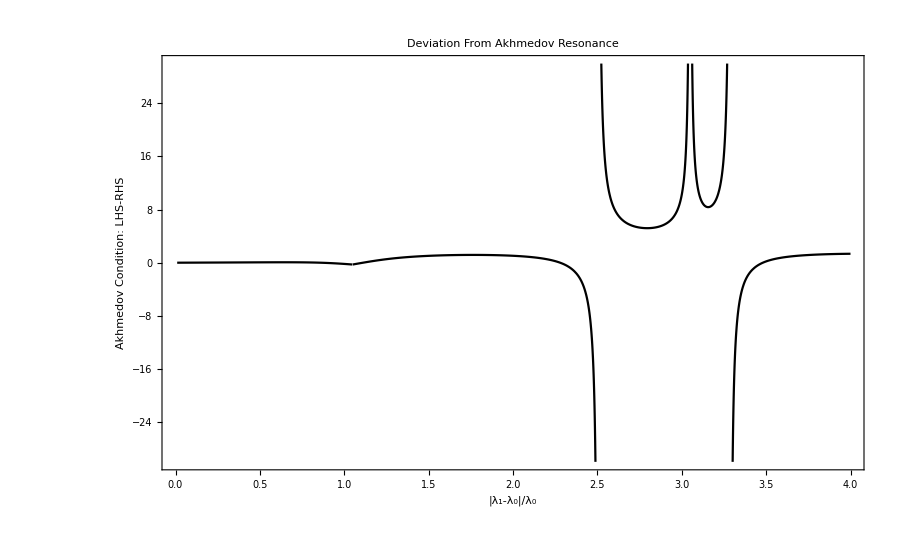

```mathematica
akhmedovConditionDeviationPlt=Plot[deviationAkhmedov[lambda0N(1-x),lambda0N(1+x)],{x,0.01,4},Frame->True,Axes->False,ImageSize->imgsize,PlotStyle->Black,PlotLabel->"Deviation From Akhmedov Resonance",FrameLabel->{"|λ_1-λ_0|/λ_0","Akhmedov Condition: LHS-RHS"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},PlotRange->{Automatic,{0-30,30}}]
```

```mathematica
(*Export["../ipynb/papers/assets/parametric-resonance/akhmedovConditionDeviationPlt.pdf",akhmedovConditionDeviationPlt]
Export["../ipynb/papers/assets/parametric-resonance/akhmedovConditionDeviationPlt.png",akhmedovConditionDeviationPlt]*)
```

Matter profile

```mathematica
lambda0N/2
```

0.421055

```mathematica
ladaEvenRecon2[x_]:=Re@ladaEvenRecon[lambda1N,lambda2N,Pi,Pi,Table[i,{i,1,1}],x]+ladaEvenCoeff0[lambda1N,lambda2N,Pi,Pi]/2
```

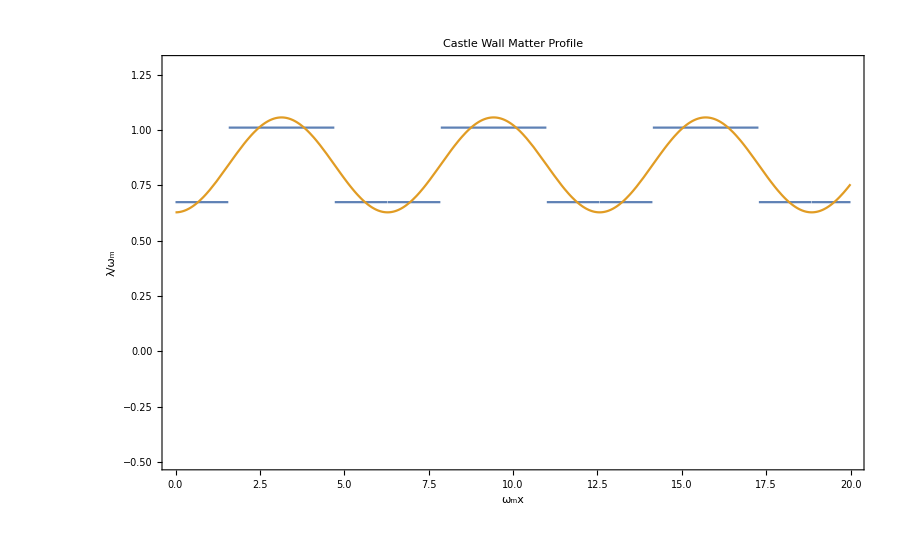

```mathematica
Plot[{ladaEven[lambda1N,lambda2N,Pi,Pi,x],ladaEvenRecon2[x]},{x,0,20},Frame->True,LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},ImageSize->imgsize,PlotLabel->"Castle Wall Matter Profile",FrameLabel->{"ω_mx","λ/ω_m"},ImagePadding->{{Automatic, 15}, {Automatic, 15}},PlotRange->{Automatic,{-0.5,1.3}}]
(*Export["../ipynb/papers/assets/parametric-resonance/castle-wall-matter-profile-0.8-0.88.png",%]*)
```

Hamiltonian

```mathematica
hamilAkhmedov[x_]:=-PauliMatrix[3]/2+1/2(ladaEven[lambda1N,lambda2N,Pi,Pi,x]-lambda0N) Cos[2thetaM] PauliMatrix[3]-1/2(ladaEven[lambda1N,lambda2N,Pi,Pi,x]-lambda0N)Sin[2thetaM] PauliMatrix[1]
hamilAkhmedovRecon2[x_]:=-PauliMatrix[3]/2+1/2(ladaEvenRecon2[x]-lambda0N)Cos[2thetaM]PauliMatrix[3]-1/2(ladaEvenRecon2[x]-lambda0N)Sin[2thetaM]PauliMatrix[1]
hamilAkhmedovRecon2No3[x_]:=-PauliMatrix[3]/2-1/2(ladaEvenRecon2[x]-lambda0N)Sin[2thetaM]PauliMatrix[1]
(*hamilAkhmedovRabi[x_,n_]:=-PauliMatrix[3]/2*)
```

```mathematica
waveAkh[x_]={waveAkh1[x],waveAkh2[x]};
```

```mathematica
initwaveAkh={1,0}
```

{1,0}

```mathematica
solAkh=NDSolve[{I D[waveAkh[x],x]==hamilAkhmedov[x].waveAkh[x],waveAkh[0]==initwaveAkh},waveAkh[x],{x,0,endpoint}];
```

```mathematica
solAkhRecon2=NDSolve[{I D[waveAkh[x],x]==hamilAkhmedovRecon2[x].waveAkh[x],waveAkh[0]==initwaveAkh},waveAkh[x],{x,0,endpoint}];
solAkhRecon2No3=NDSolve[{I D[waveAkh[x],x]==hamilAkhmedovRecon2No3[x].waveAkh[x],waveAkh[0]==initwaveAkh},waveAkh[x],{x,0,endpoint}];
```

```mathematica
solAkh
```

{{waveAkh1[x]→InterpolatingFunction[{{0., 15000.}}, <>][x],waveAkh2[x]→InterpolatingFunction[{{0., 15000.}}, <>][x]}}

```mathematica
solAkhList=Table[{x,Abs[waveAkh2[x]]^2/.First@solAkh},{x,0,endpoint/50,0.01}];
solAkhRecon2List=Table[{x,Abs[waveAkh2[x]]^2/.First@solAkhRecon2},{x,0,endpoint/100,0.01}];
solAkhRecon2No3List=Table[{x,Abs[waveAkh2[x]]^2/.First@solAkhRecon2No3},{x,0,endpoint/100,0.01}];
(* Change the range endpoint/5000 for different cases: *)
```

Theory prediction of this resonance, assuming the resonance is generated only by the one mode

```mathematica
rD[a1_,a2_,k2_]:=Abs[a2^2/(2a1(1-k2))]
rD2[a1_,a2_,k1_,k2_,omm_:1]:=Abs[(k1-omm)/a1+a2^2/(2a1(omm-k2))]
```

```mathematica
probAkhmedovRabiTheory[x_]:=Sin[ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]x/4]^2;
probAkhmedovRabiTheory2[a1_,a2_,k2_,x_]:=1/(1+rD[a1,a2,k2]^2)Sin[a1 √(1+rD[a1,a2,k2]^2) x/2]^2;
probAkhmedovRabiTheory3[a1_,x_]:=Sin[a1 x/2]^2;
ampAkhmedovRabiTheory[a1_,a2_,k1_,k2_]:=1/(1+rD[a1,a2,k2]^2)
```

```mathematica
ladaEvenCoeff0[lambda1N,lambda2N,Pi,Pi]
ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2
ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,3]
ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,5]
Sin[2thetaM]
```

1.68422

-0.0415425

0.0714804

-0.0428883

0.387449

```mathematica
rD[ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2,ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2,ladaknEven[lambda1N,lambda2N,Pi,Pi,3]]
```

0.00115396

```mathematica
rD2[ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2,ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2,ladaknEven[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2,ladaknEven[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2]
```

19.4029

```mathematica
2Pi/(ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2)

Tan[2thetaM]BesselJ[1,Cos[2thetaM]ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2]
Tan[2thetaM]Cos[2thetaM]ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2/2

2 Tan[2thetaM]BesselJ[2,Cos[2thetaM]ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2]

ladaEvenRecon2[x]
ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]

hamilAkhmedovRecon2No3[x]
```

-151.247

-0.00804633

-0.00804781

0.000154087

0.842109-0.214441 Re[Cos[x]]

-0.214441

{{-0.5,-0.193725 (0.-0.214441 Re[Cos[x]])},{-0.193725 (0.-0.214441 Re[Cos[x]]),0.5}}

```mathematica
probAkhmedovRabiTheory2[ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2,ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2,ladaknEven[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2,x]
```

0.99997 Sin[0.0207716 x]^2

```mathematica
probAkhmedovRabiTheoryList=Table[{x,probAkhmedovRabiTheory[x]},{x,0,endpoint/100,0.1}];
(* Change the range endpoint/5000 for different cases: *)
```

```mathematica
probAkhmedovRabiTheory2List=Table[{x,probAkhmedovRabiTheory2[ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2,ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2,ladaknEven[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2,x]},{x,0,endpoint/100,0.1}];

probAkhmedovRabiTheory3List=Table[{x,probAkhmedovRabiTheory3[ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2,x]},{x,0,endpoint/50,1}];
```

```mathematica
N[thetaV,1]
```

0.154948

```mathematica
akhmedovOscPlt=ListPlot[{solAkhList,solAkhRecon2List,solAkhRecon2No3List,probAkhmedovRabiTheory3List},Joined->{True,True},PlotMarkers->{""," ","  ",{"○",11},{"+",18}},PlotStyle->{Black,Directive[Red,Dashed]},Frame->True,ImageSize->imgsize*1.1,PlotLabel->"Transition Probability For a Castle Wall Matter Profile",FrameLabel->{"ω_mx","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},PlotRange->{{0,endpoint/50},Automatic},ImagePadding->{{Automatic, 15}, {Automatic, 15}},PlotLegends->Placed[{"Numerical Solution of Castle Profile","Using only 1st Fourier Mode","Without Varying Sigma3","Prediction Using Rabi Formula"},{Center,Below}],Epilog->Inset[Style["δm^2="<>deltamsquare13String<>" MeV^2\n θ_v="<>ToString[NumberForm[thetaV,3]]<>"\n E="<>ToString[energy10]<>"MeV",FontSize->14],{10,0.8},{Left,Top}]]
```

-Graphics-

```mathematica
(*Export["../ipynb/papers/assets/parametric-resonance/akhmedovOscPlt.pdf",akhmedovOscPlt]
Export["../ipynb/papers/assets/parametric-resonance/akhmedovOscPlt.png",akhmedovOscPlt]*)
```

Export data list

```mathematica
filenamelabel=ToString[2*lambdaDFrachalf]
(*StringReplace[ToString[lambdaDFrachalf*2]," "->""]*)
```

0.4

```mathematica
Export["../ipynb/papers/assets/parametric-resonance/solAkhList-"<>filenamelabel<>".csv",solAkhList]
Export["../ipynb/papers/assets/parametric-resonance/probAkhmedovRabiTheoryList-"<>filenamelabel<>".csv",probAkhmedovRabiTheory3List]
```

../ipynb/papers/assets/parametric-resonance/solAkhList-0.4.csv

../ipynb/papers/assets/parametric-resonance/probAkhmedovRabiTheoryList-0.4.csv

```mathematica
Style["δm^2="<>deltamsquare13String<>" MeV^2\n θ_v="<>ToString[NumberForm[thetaV,3]]<>"\n E="<>ToString[energy10]<>"MeV",FontSize->14]
```

δm^2=2.6*e-15 MeV^2
 θ_v=0.155
 E=10MeV

```mathematica
Sin[2thetaV]^2
```

0.093

```mathematica
ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]
```

-0.00673687

## Calculate the Q values for each mode

Refer tot he paper for the details.

```mathematica
qnmode[n_,alpha_,thetavac_,thetamatter_]:=2(2n-1)(n-1)Pi  √(1+3Sin[2thetavac]^2)/(alpha Cos[2thetavac]Sin[2thetamatter])
```

```mathematica
Table[qnmode[i,0.003Pi,thetaV,thetaM],{i,1,4}]
Table[qnmode[i,3.065Pi,thetaV,thetaM],{i,1,4}]
```

{0.,6129.81,20432.7,42908.7}

{0.,5.99981,19.9994,41.9987}

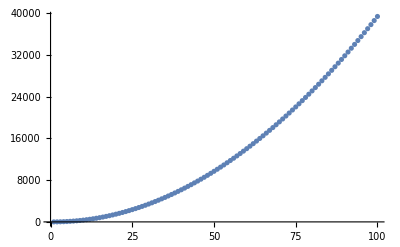

```mathematica
ListPlot[Table[qnmode[i,3.065Pi,thetaV,thetaM],{i,1,100}]]
```

## The Second Frequency is way to off resonance

Build the necessary parameters

```mathematica
k0CW=2Pi/(2Pi);
kListCW=Table[{(2i-1)k0CW},{i,1,10}]
aListCW=Table[{2/((2i-1)Pi)(-1)^i 2lambdaD},{i,1,10}]
```

{{1},{3},{5},{7},{9},{11},{13},{15},{17},{19}}

{{-0.214441},{0.0714804},{-0.0428883},{0.0306345},{-0.0238268},{0.0194947},{-0.0164955},{0.0142961},{-0.0126142},{0.0112864}}

So we need Jacobi-Anger Expansion, the coefficients are

```mathematica
rD[ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Sin[2thetaM]/2,ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,3]Sin[2thetaM]/2,ladaknEven[lambda1N,lambda2N,Pi,Pi,3]]
```

0.00115396

Consider only the first frequency

```mathematica
qvalueListCW=qValueOrderdList[listNGenerator[1,3],kListCW[[1]],aListCW[[1]],{0},thetaM]
neuWidthListCW=Table[widthNList[qvalueListCW[[i,1]],kListCW[[1]],aListCW[[1]],{0},thetaM],
{i,1,Length@qvalueListCW}];
neuGridListCW=Table[{qvalueListCW[[i,1]],
qvalueListCW[[i,2]],
neuWidthListCW[[i]],
qvalueListCW[[1,2]]+neuWidthListCW[[i]]/(2 neuWidthListCW[[1]]qvalueListCW[[i,2]]),
Pi/(neuWidthListCW[[i]]^2+(1-qvalueListCW[[i,1]].{kListCW[[1]]})^2)^(1/2)},
{i,1,Length@qvalueListCW}];
PrependTo[neuGridListCW,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelength"}];
Grid@neuGridListCW
```

{{{1},0.},{{-1},48.3794},{{2},244.323},{{-2},732.968},{{3},9878.97},{{-3},19757.9},{{0},ComplexInfinity}}

Power::infy: Infinite expression 1/0. encountered.

{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelength
{1} | 0. | 0.0413399 | ComplexInfinity | {75.9942}
{-1} | 48.3794 | 0.0413399 | 0.010335 | {1.57046}
{2} | 244.323 | 0.00409295 | 0.000202616 | {3.14157}
{-2} | 732.968 | 0.00409295 | 0.0000675385 | {1.0472}
{3} | 9878.97 | 0.00020245 | 2.4786×10^-7 | {1.5708}
{-3} | 19757.9 | 0.00020245 | 1.2393×10^-7 | {0.785398}
{0} | ComplexInfinity | 0. | 0. | {3.14159}

Now consider the first two frequencies

```mathematica
index4significant2=2;
qvalueList2CW=qValueOrderdList[listNGenerator[2,3],Join[kListCW[[1]],kListCW[[2]]],Join[aListCW[[1]],aListCW[[2]]],{0,0},thetaM];
neuWidthList2CW=Table[widthNList[qvalueList2CW[[i,1]],Join[kListCW[[1]],kListCW[[2]]],Join[aListCW[[1]],aListCW[[2]]],{0,0},thetaM],
{i,1,Length@qvalueList2CW}];
neuGridList2CW=Table[{qvalueList2CW[[i,1]],
qvalueList2CW[[i,2]],
neuWidthList2CW[[i]],
qvalueList2CW[[index4significant2,2]]+neuWidthList2CW[[i]]/(2 neuWidthList2CW[[index4significant2]]qvalueList2CW[[i,2]]),
Pi/(neuWidthList2CW[[i]]^2+(1-qvalueList2CW[[i,1]].Join[kListCW[[1]],kListCW[[2]]])^2)^(1/2)},
{i,1,Length@qvalueList2CW}];
PrependTo[neuGridList2CW,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelength"}];
Grid@neuGridList2CW
```

Power::infy: Infinite expression 1/0. encountered.

{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelength
{-2,1} | 0. | 0.0000224748 | ComplexInfinity | 139783.
{1,0} | 0. | 0.0413349 | ComplexInfinity | 76.0033
{-1,0} | 48.3852 | 0.0413349 | 0.0103337 | 1.57046
{0,1} | 145.861 | 0.0137117 | 0.00113712 | 1.57076
{2,0} | 244.352 | 0.00409245 | 0.000202591 | 3.14157
{0,-1} | 291.721 | 0.0137117 | 0.00056856 | 0.785394
{-2,0} | 733.057 | 0.00409245 | 0.0000675304 | 1.0472
{-1,1} | 1101.31 | 0.000908007 | 9.97312×10^-6 | 3.14159
{1,1} | 1651.97 | 0.00181601 | 0.0000132975 | 1.0472
{-1,-1} | 2753.28 | 0.00181601 | 7.97849×10^-6 | 0.628318
{1,-1} | 3303.94 | 0.000908007 | 3.32437×10^-6 | 1.0472
{3,0} | 9880.16 | 0.000202426 | 2.4783×10^-7 | 1.5708
{-3,0} | 19760.3 | 0.000202426 | 1.23915×10^-7 | 0.785398
{0,2} | 33201.2 | 0.000150597 | 5.48675×10^-8 | 0.628319
{2,1} | 35595.4 | 0.000112374 | 3.81877×10^-8 | 0.785398
{0,-2} | 46481.7 | 0.000150597 | 3.91911×10^-8 | 0.448799
{-2,-1} | 53393.2 | 0.000112374 | 2.54585×10^-8 | 0.523599
{2,-1} | 88988.6 | 0.0000224748 | 3.05502×10^-9 | 1.5708
{-1,2} | 320875. | 0.0000124659 | 4.69937×10^-10 | 0.785398
{1,2} | 343795. | 0.0000174523 | 6.14051×10^-10 | 0.523599
{-1,-2} | 458394. | 0.0000174523 | 4.60538×10^-10 | 0.392699
{1,-2} | 481313. | 0.0000124659 | 3.13291×10^-10 | 0.523599
{3,1} | 1.12443×10^6 | 4.4467×10^-6 | 4.78363×10^-11 | 0.628319
{-3,-1} | 1.5742×10^6 | 4.4467×10^-6 | 3.41688×10^-11 | 0.448799
{-2,2} | 6.07675×10^6 | 4.93685×10^-7 | 9.82724×10^-13 | 1.0472
{2,2} | 7.08954×10^6 | 9.8737×10^-7 | 1.68467×10^-12 | 0.448799
{-2,-2} | 9.11512×10^6 | 9.8737×10^-7 | 1.3103×10^-12 | 0.349066
{0,3} | 9.6735×10^6 | 8.27001×10^-7 | 1.03413×10^-12 | 0.392699
{2,-2} | 1.01279×10^7 | 4.93685×10^-7 | 5.89634×10^-13 | 0.628319
{0,-3} | 1.20919×10^7 | 8.27001×10^-7 | 8.27304×10^-13 | 0.314159
{-1,3} | 9.58641×10^7 | 7.30201×10^-8 | 9.21381×10^-15 | 0.448799
{1,3} | 9.8603×10^7 | 9.12751×10^-8 | 1.11973×10^-14 | 0.349066
{-1,-3} | 1.20515×10^8 | 9.12751×10^-8 | 9.16145×10^-15 | 0.285599
{1,-3} | 1.23254×10^8 | 7.30201×10^-8 | 7.16629×10^-15 | 0.349066
{-3,2} | 1.63805×10^8 | 1.22096×10^-8 | 9.01627×10^-16 | 1.5708
{3,2} | 2.18407×10^8 | 3.66288×10^-8 | 2.02866×10^-15 | 0.392699
{-3,-2} | 2.73009×10^8 | 3.66288×10^-8 | 1.62293×10^-15 | 0.314159
{3,-2} | 3.27611×10^8 | 1.22096×10^-8 | 4.50813×10^-16 | 0.785398
{-2,3} | 1.89699×10^9 | 3.16291×10^-9 | 2.01686×10^-17 | 0.523599
{2,3} | 2.01196×10^9 | 4.97029×10^-9 | 2.98824×10^-17 | 0.314159
{-2,-3} | 2.41435×10^9 | 4.97029×10^-9 | 2.4902×10^-17 | 0.261799
{2,-3} | 2.52932×10^9 | 3.16291×10^-9 | 1.51264×10^-17 | 0.392699
{-3,3} | 5.59293×10^10 | 8.93986×10^-11 | 1.9335×10^-20 | 0.628319
{3,3} | 6.15222×10^10 | 1.78797×10^-10 | 3.51545×10^-20 | 0.285599
{-3,-3} | 7.27081×10^10 | 1.78797×10^-10 | 2.97462×10^-20 | 0.241661
{3,-3} | 7.8301×10^10 | 8.93986×10^-11 | 1.38107×10^-20 | 0.448799
{-3,1} | ComplexInfinity | 0. | 0. | 3.14159
{0,0} | ComplexInfinity | 0. | 0. | 3.14159
{3,-1} | ComplexInfinity | 0. | 0. | 3.14159

```mathematica
index4significant3=10;
qvalueList3CW=qValueOrderdList[listNGenerator[3,4],Join[kListCW[[1]],kListCW[[2]],kListCW[[3]]],Join[aListCW[[1]],aListCW[[2]],aListCW[[3]]],{0,0,0},thetaM];
neuWidthList3CW=Table[widthNList[qvalueList3CW[[i,1]],Join[kListCW[[1]],kListCW[[2]],kListCW[[3]]],Join[aListCW[[1]],aListCW[[2]],aListCW[[3]]],{0,0,0},thetaM],
{i,1,Length@qvalueList3CW}];
neuGridList3CW=Table[{qvalueList3CW[[i,1]],
qvalueList3CW[[i,2]],
neuWidthList3CW[[i]],
qvalueList3CW[[index4significant3,2]]+neuWidthList3CW[[i]]/(2 neuWidthList3CW[[index4significant3]]qvalueList3CW[[i,2]]),
Pi/(neuWidthList3CW[[i]]^2+(1-qvalueList3CW[[i,1]].Join[kListCW[[1]],kListCW[[2]],kListCW[[3]]])^2)^(1/2)},
{i,1,Length@qvalueList3CW}];
PrependTo[neuGridList3CW,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelength"}];
Grid@neuGridList3CW[[1;;30]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelength
{-4,0,1} | 0. | 6.59583×10^-9 | ComplexInfinity | 4.763×10^8
{-3,-2,2} | 0. | 3.18115×10^-14 | ComplexInfinity | 9.87564×10^13
{-3,3,-1} | 0. | 5.89107×10^-14 | ComplexInfinity | 5.3328×10^13
{-2,-4,3} | 0. | 1.27805×10^-20 | ComplexInfinity | 2.45811×10^20
{-2,1,0} | 0. | 0.0000224744 | ComplexInfinity | 139785.
{-1,-1,1} | 0. | 1.79504×10^-6 | ComplexInfinity | 1.75015×10^6
{-1,4,-2} | 0. | 1.95891×10^-16 | ComplexInfinity | 1.60375×10^16
{0,-3,2} | 0. | 7.18237×10^-13 | ComplexInfinity | 4.37403×10^12
{0,2,-1} | 0. | 9.92384×10^-8 | ComplexInfinity | 3.1657×10^7
{1,0,0} | 0. | 0.0413343 | ComplexInfinity | 76.0045
{2,-2,1} | 0. | 4.87983×10^-10 | ComplexInfinity | 6.43791×10^9
{2,3,-2} | 0. | 3.53177×10^-15 | ComplexInfinity | 8.89523×10^14
{3,-4,2} | 0. | 3.19773×10^-19 | ComplexInfinity | 9.82445×10^18
{3,1,-1} | 0. | 2.93023×10^-9 | ComplexInfinity | 1.07213×10^9
{4,-1,0} | 0. | 1.83227×10^-8 | ComplexInfinity | 1.71459×10^8
{4,4,-3} | 0. | 1.04196×10^-23 | ComplexInfinity | 3.01509×10^23
{-1,0,0} | 48.386 | 0.0413343 | 0.0103336 | 1.57046
{0,1,0} | 145.863 | 0.0137115 | 0.0011371 | 1.57076
{2,0,0} | 244.356 | 0.00409239 | 0.000202588 | 3.14157
{0,-1,0} | 291.726 | 0.0137115 | 0.000568551 | 0.785394
{0,0,1} | 486.235 | 0.00822647 | 0.000204657 | 0.785397
{0,0,-1} | 729.353 | 0.00822647 | 0.000136438 | 0.523598
{-2,0,0} | 733.068 | 0.00409239 | 0.0000675293 | 1.0472
{-1,1,0} | 1101.33 | 0.000907993 | 9.97296×10^-6 | 3.14159
{1,1,0} | 1652. | 0.00181599 | 0.0000132973 | 1.0472
{-1,-1,0} | 2753.33 | 0.00181599 | 7.97837×10^-6 | 0.628318
{1,-1,0} | 3303.99 | 0.000907993 | 3.32432×10^-6 | 1.0472
{-1,0,1} | 4589.12 | 0.00065372 | 1.72315×10^-6 | 1.0472
{1,0,1} | 5099.02 | 0.000980581 | 2.32625×10^-6 | 0.628319

```mathematica
Module[{},
index4significant10=64;
len=4;

qvalueList10CW=qValueOrderdList[listNGenerator[len,4],Flatten@kListCW[[1;;len]],Flatten@aListCW[[1;;len]],ConstantArray[0,len],thetaM];
neuWidthList10CW=Table[widthNList[qvalueList10CW[[i,1]],Flatten@kListCW[[1;;len]],Flatten@aListCW[[1;;len]],ConstantArray[0,len],thetaM],
{i,1,Length@qvalueList10CW}];
neuGridList10CW=Table[{qvalueList10CW[[i,1]],
qvalueList10CW[[i,2]],
neuWidthList10CW[[i]],
qvalueList10CW[[index4significant10,2]]+neuWidthList10CW[[i]]/(2 neuWidthList10CW[[index4significant10]]qvalueList10CW[[i,2]]),
Pi/(neuWidthList10CW[[i]]^2+(1-qvalueList10CW[[i,1]].Flatten@kListCW[[1;;len]])^2)^(1/2)},
{i,1,Length@qvalueList10CW}];
PrependTo[neuGridList10CW,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelength"}];
Grid@neuGridList10CW[[60;;200]]
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{1,-3,-1,2} | 0. | 7.34278×10^-17 | ComplexInfinity | 4.27848×10^16
{1,-2,-3,3} | 0. | 3.5139×10^-23 | ComplexInfinity | 8.94047×10^22
{1,-2,4,-2} | 0. | 5.16543×10^-23 | ComplexInfinity | 6.08195×10^22
{1,-1,2,-1} | 0. | 7.15854×10^-12 | ComplexInfinity | 4.3886×10^11
{1,0,0,0} | 0. | 0.0413341 | ComplexInfinity | 76.0048
{1,1,-2,1} | 0. | 7.15854×10^-12 | ComplexInfinity | 4.3886×10^11
{1,2,-4,2} | 0. | 5.16543×10^-23 | ComplexInfinity | 6.08195×10^22
{1,2,3,-3} | 0. | 3.5139×10^-23 | ComplexInfinity | 8.94047×10^22
{1,3,1,-2} | 0. | 7.34278×10^-17 | ComplexInfinity | 4.27848×10^16
{1,4,-1,-1} | 0. | 1.99888×10^-16 | ComplexInfinity | 1.57168×10^16
{2,-4,-2,3} | 0. | 1.32674×10^-26 | ComplexInfinity | 2.36791×10^26
{2,-3,-4,4} | 0. | 3.17457×10^-33 | ComplexInfinity | 9.89611×10^32
{2,-3,3,-1} | 0. | 9.38969×10^-21 | ComplexInfinity | 3.34579×10^20
{2,-2,1,0} | 0. | 4.87981×10^-10 | ComplexInfinity | 6.43794×10^9
{2,-1,-1,1} | 0. | 1.79255×10^-10 | ComplexInfinity | 1.75258×10^10
{2,0,-3,2} | 0. | 4.28893×10^-17 | ComplexInfinity | 7.32489×10^16
{2,0,4,-3} | 0. | 2.85068×10^-23 | ComplexInfinity | 1.10205×10^23
{2,1,2,-2} | 0. | 3.57432×10^-16 | ComplexInfinity | 8.78935×10^15
{2,2,0,-1} | 0. | 2.48968×10^-10 | ComplexInfinity | 1.26184×10^10
{2,3,-2,0} | 0. | 3.53176×10^-15 | ComplexInfinity | 8.89527×10^14
{2,4,-4,1} | 0. | 2.5484×10^-26 | ComplexInfinity | 1.23277×10^26
{2,4,3,-4} | 0. | 8.8183×10^-33 | ComplexInfinity | 3.56258×10^32
{3,-4,2,0} | 0. | 3.19772×10^-19 | ComplexInfinity | 9.82449×10^18
{3,-3,0,1} | 0. | 3.00562×10^-14 | ComplexInfinity | 1.04524×10^14
{3,-2,-2,2} | 0. | 6.47259×10^-20 | ComplexInfinity | 4.85369×10^19
{3,-1,-4,3} | 0. | 1.03248×10^-26 | ComplexInfinity | 3.04277×10^26
{3,-1,3,-2} | 0. | 1.55339×10^-20 | ComplexInfinity | 2.02241×10^20
{3,0,1,-1} | 0. | 5.38171×10^-10 | ComplexInfinity | 5.83753×10^9
{3,1,-1,0} | 0. | 2.93021×10^-9 | ComplexInfinity | 1.07214×10^9
{3,2,-3,1} | 0. | 8.45753×10^-20 | ComplexInfinity | 3.71455×10^19
{3,2,4,-4} | 0. | 2.85942×10^-32 | ComplexInfinity | 1.09868×10^32
{3,3,2,-3} | 0. | 1.59337×10^-25 | ComplexInfinity | 1.97166×10^25
{3,4,0,-2} | 0. | 8.32385×10^-20 | ComplexInfinity | 3.7742×10^19
{4,-4,-1,2} | 0. | 8.13685×10^-24 | ComplexInfinity | 3.86094×10^23
{4,-3,-3,3} | 0. | 5.19189×10^-30 | ComplexInfinity | 6.05096×10^29
{4,-3,4,-2} | 0. | 7.63209×10^-30 | ComplexInfinity | 4.1163×10^29
{4,-2,2,-1} | 0. | 1.58656×10^-18 | ComplexInfinity | 1.98013×10^18
{4,-1,0,0} | 0. | 1.83226×10^-8 | ComplexInfinity | 1.7146×10^8
{4,0,-2,1} | 0. | 2.63039×10^-14 | ComplexInfinity | 1.19434×10^14
{4,1,-4,2} | 0. | 3.79621×10^-25 | ComplexInfinity | 8.2756×10^24
{4,1,3,-3} | 0. | 2.58245×10^-25 | ComplexInfinity | 1.21651×10^25
{4,2,1,-2} | 0. | 8.09467×10^-19 | ComplexInfinity | 3.88106×10^18
{4,3,-1,-1} | 0. | 2.93809×10^-18 | ComplexInfinity | 1.06926×10^18
{4,4,-3,0} | 0. | 1.04195×10^-23 | ComplexInfinity | 3.0151×10^23
{-1,0,0,0} | 48.3862 | 0.0413341 | 5.96669×10^7 | 1.57046
{0,1,0,0} | 145.863 | 0.0137114 | 6.56572×10^6 | 1.57076
{2,0,0,0} | 244.357 | 0.00409237 | 1.16976×10^6 | 3.14157
{0,-1,0,0} | 291.727 | 0.0137114 | 3.28286×10^6 | 0.785394
{0,0,1,0} | 486.237 | 0.00822644 | 1.18171×10^6 | 0.785397
{0,0,-1,0} | 729.356 | 0.00822644 | 787804. | 0.523598
{-2,0,0,0} | 733.071 | 0.00409237 | 389920. | 1.0472
{0,0,0,1} | 1021.1 | 0.00587599 | 401936. | 0.523599
{-1,1,0,0} | 1101.33 | 0.000907989 | 57584.7 | 3.14159
{0,0,0,-1} | 1361.47 | 0.00587599 | 301452. | 0.392699
{1,1,0,0} | 1652. | 0.00181598 | 76779.6 | 1.0472
{-1,-1,0,0} | 2753.34 | 0.00181598 | 46067.7 | 0.628318
{1,-1,0,0} | 3304. | 0.000907989 | 19194.9 | 1.0472
{-1,0,1,0} | 4589.14 | 0.000653718 | 9949.59 | 1.0472
{1,0,1,0} | 5099.04 | 0.000980577 | 13431.9 | 0.628319
{-1,0,-1,0} | 7138.66 | 0.000980577 | 9594.24 | 0.448799
{1,0,-1,0} | 7648.56 | 0.000653718 | 5969.75 | 0.628319
{3,0,0,0} | 9880.36 | 0.000202422 | 1430.97 | 1.5708
{-1,0,0,1} | 9994.18 | 0.000500291 | 3496.4 | 0.628319
{1,0,0,1} | 10493.9 | 0.000667055 | 4439.88 | 0.448799
{-1,0,0,-1} | 13492.1 | 0.000667055 | 3453.24 | 0.349066
{1,0,0,-1} | 13991.8 | 0.000500291 | 2497.43 | 0.448799
{-3,0,0,0} | 19760.7 | 0.000202422 | 715.485 | 0.785398
{0,-1,1,0} | 27668.5 | 0.0000361421 | 91.2374 | 3.14159
{0,2,0,0} | 33201.8 | 0.000150594 | 316.804 | 0.628319
{2,1,0,0} | 35596.1 | 0.000112372 | 220.496 | 0.785398
{0,-2,0,0} | 46482.6 | 0.000150594 | 226.289 | 0.448799
{0,1,1,0} | 48420. | 0.000144568 | 208.543 | 0.448799
{-2,-1,0,0} | 53394.2 | 0.000112372 | 146.997 | 0.523599
{0,-1,-1,0} | 62254.2 | 0.000144568 | 162.2 | 0.349066
{0,-1,0,1} | 81346. | 0.0000368795 | 31.6661 | 1.0472
{-2,0,1,0} | 82402.8 | 0.000024271 | 20.5727 | 1.5708
{0,1,-1,0} | 83005.6 | 0.0000361421 | 30.4125 | 1.0472
{2,-1,0,0} | 88990.4 | 0.0000224743 | 17.6396 | 1.5708
{0,1,0,1} | 97615.2 | 0.0000921988 | 65.971 | 0.349066
{2,0,1,0} | 105946. | 0.0000566324 | 37.3357 | 0.523599
{0,-1,0,-1} | 119307. | 0.0000921988 | 53.9763 | 0.285599
{0,1,0,-1} | 135577. | 0.0000368795 | 18.9997 | 0.628319
{-2,0,-1,0} | 141262. | 0.0000566324 | 28.0018 | 0.392699
{0,0,-1,1} | 150649. | 6.63796×10^-6 | 3.07762 | 3.14159
{2,0,-1,0} | 164806. | 0.000024271 | 10.2864 | 0.785398
{-2,0,0,1} | 193813. | 0.0000206385 | 7.43776 | 0.785398
{2,0,0,1} | 215347. | 0.0000371493 | 12.0492 | 0.392699
{-2,0,0,-1} | 269184. | 0.0000371493 | 9.63934 | 0.314159
{0,0,1,1} | 276189. | 0.0000398278 | 10.0722 | 0.285599
{0,0,2,0} | 276701. | 0.000032526 | 8.21042 | 0.349066
{2,0,0,-1} | 290719. | 0.0000206385 | 4.95851 | 0.523599
{-1,2,0,0} | 320882. | 0.0000124656 | 2.71341 | 0.785398
{0,0,-1,-1} | 326405. | 0.0000398278 | 8.52264 | 0.241661
{0,0,-2,0} | 338191. | 0.000032526 | 6.71762 | 0.285599
{1,2,0,0} | 343802. | 0.0000174519 | 3.54552 | 0.523599
{1,-1,1,0} | 371396. | 5.38509×10^-6 | 1.01275 | 1.5708
{4,0,0,0} | 449588. | 6.67277×10^-6 | 1.03666 | 1.0472
{0,0,1,-1} | 451946. | 6.63796×10^-6 | 1.02587 | 1.0472
{-1,-2,0,0} | 458403. | 0.0000174519 | 2.65914 | 0.392699
{-1,1,1,0} | 477509. | 0.0000125652 | 1.83795 | 0.523599
{1,-2,0,0} | 481323. | 0.0000124656 | 1.80894 | 0.523599
{1,1,1,0} | 495194. | 0.0000161553 | 2.27869 | 0.392699
{-1,-1,-1,0} | 618993. | 0.0000161553 | 1.82295 | 0.314159
{1,-1,-1,0} | 636678. | 0.0000125652 | 1.37847 | 0.392699
{-1,-1,0,1} | 727939. | 2.74748×10^-6 | 0.263624 | 1.5708
{-1,1,-1,0} | 742791. | 5.38509×10^-6 | 0.506375 | 0.785398
{-4,0,0,0} | 749313. | 6.67277×10^-6 | 0.621998 | 0.628319
{1,-1,0,1} | 873527. | 4.57914×10^-6 | 0.366145 | 0.785398
{-1,1,0,1} | 970586. | 8.24244×10^-6 | 0.593154 | 0.392699
{1,1,0,1} | 992645. | 0.0000100741 | 0.708856 | 0.314159
{0,0,0,2} | 1.09673×10^6 | 0.0000118534 | 0.7549 | 0.241661
{1,1,-1,0} | 1.11419×10^6 | 1.79503×10^-6 | 0.112528 | 1.5708
{3,1,0,0} | 1.12445×10^6 | 4.44661×10^-6 | 0.276207 | 0.628319
{-1,-1,0,-1} | 1.19117×10^6 | 0.0000100741 | 0.590713 | 0.261799
{1,-1,0,-1} | 1.21323×10^6 | 8.24244×10^-6 | 0.474524 | 0.314159
{0,0,0,-2} | 1.26546×10^6 | 0.0000118534 | 0.654247 | 0.20944
{-1,1,0,-1} | 1.31029×10^6 | 4.57914×10^-6 | 0.244096 | 0.523599
{1,1,0,-1} | 1.45588×10^6 | 2.74748×10^-6 | 0.131812 | 0.785398
{-3,-1,0,0} | 1.57423×10^6 | 4.44661×10^-6 | 0.19729 | 0.448799
{-3,0,1,0} | 1.87418×10^6 | 5.33565×10^-7 | 0.0198848 | 3.14159
{1,0,-1,1} | 2.02216×10^6 | 9.89041×10^-7 | 0.0341621 | 1.5708
{-1,0,2,0} | 2.75124×10^6 | 2.90778×10^-6 | 0.073821 | 0.392699
{-1,0,1,1} | 2.75749×10^6 | 3.62648×10^-6 | 0.0918581 | 0.314159
{1,0,1,1} | 2.79991×10^6 | 4.28585×10^-6 | 0.106915 | 0.261799
{1,0,2,0} | 2.81376×10^6 | 3.55396×10^-6 | 0.0882206 | 0.314159
{-1,0,-1,-1} | 3.26657×10^6 | 4.28585×10^-6 | 0.0916412 | 0.224399
{3,0,1,0} | 3.27982×10^6 | 2.13426×10^-6 | 0.0454509 | 0.448799
{1,0,-1,-1} | 3.30899×10^6 | 3.62648×10^-6 | 0.0765484 | 0.261799
{-1,0,-2,0} | 3.37652×10^6 | 3.55396×10^-6 | 0.0735172 | 0.261799
{1,0,-2,0} | 3.43905×10^6 | 2.90778×10^-6 | 0.0590568 | 0.314159
{-1,0,1,-1} | 4.04432×10^6 | 9.89041×10^-7 | 0.0170811 | 0.785398
{-3,0,-1,0} | 4.21692×10^6 | 2.13426×10^-6 | 0.0353507 | 0.349066
{-3,0,0,1} | 5.51014×10^6 | 5.44451×10^-7 | 0.00690148 | 1.0472
{3,0,-1,0} | 5.62255×10^6 | 5.33565×10^-7 | 0.00662826 | 1.0472
{1,0,1,-1} | 6.06648×10^6 | 3.2968×10^-7 | 0.00379579 | 1.5708
{-2,2,0,0} | 6.07687×10^6 | 4.93675×10^-7 | 0.00567423 | 1.0472
{3,0,0,1} | 6.61216×10^6 | 1.36113×10^-6 | 0.0143781 | 0.349066
{2,2,0,0} | 7.08968×10^6 | 9.87351×10^-7 | 0.00972726 | 0.448799
{-3,0,0,-1} | 8.08153×10^6 | 1.36113×10^-6 | 0.0117639 | 0.285599
{2,-1,1,0} | 8.4402×10^6 | 3.55442×10^-7 | 0.00294145 | 1.0472
{-2,-2,0,0} | 9.1153×10^6 | 9.87351×10^-7 | 0.00756565 | 0.349066

```mathematica
castleModeB[n1_,n2_,k1_,k2_]:=Tan[2thetaM](n1 k1 + n2 k2)BesselJ[n1,ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,1]Cos[2thetaM]/k1]BesselJ[n2,ladaEvenCoeff[lambda1N,lambda2N,Pi,Pi,3]Cos[2thetaM]/k2]
```

```mathematica
castleModeB[-2,1,1,3]
castleModeB[1,0,1,3]
```

0.0000224748

-0.0413349

## Find the parameters to be used in the paper

To show that even the lowest mode is not zero, we also can have a destruction.

```mathematica
?BesselJ
```

RowBox[{"BesselJ", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the Bessel function of the first kind RowBox[{SubscriptBox[StyleBox["J", "TI"], StyleBox["n", "TI"]], "(", StyleBox["z", "TI"], ")"}].

```mathematica
bessel0[n_,lambda1_,lambda2_,x_]:=BesselJ[0,Cos[2thetaM]((-1)^n (lambda1-lambda2)x)/((2n-1)^2Pi^2)]
```

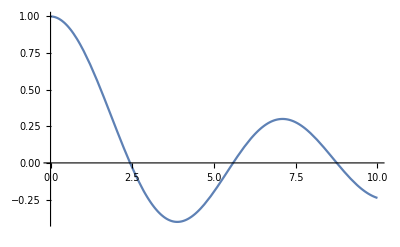

```mathematica
Plot[bessel0[1,lambda0N-delta,lambda0N+delta,2Pi]/.{delta->alpha lambda0N},{alpha,0.00001,10}]
```

```mathematica
Limit[Sum[1/(2 n-1),{n,1,x}],{x->Infinity}]
```

{∞}

```mathematica
Series[BesselJ[1,x],{x,0,3}]
```

x/2-x^3/16+O[x]^4

```mathematica
?Product
```

Product[f,{i,i_max}] evaluates the product ∏_(i=1)^i_max f. 
Product[f,{i,i_min,i_max}] starts with i=i_min. 
Product[f,{i,i_min,i_max,di}] uses steps di. 
Product[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Product[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple product ∏_(i=i_min)^i_max ∏_(j=j_min)^j_max … f. 
Product[f,i] gives the indefinite product ∏_i f.

```mathematica
Limit[Sum[n(2n-1),{n,1,lim}]Product[(-1)^n /((2n-1)^2Pi^2),{n,1,lim}],lim->Infinity]
```

Limit[((-1)^(1+lim) ⅈ^((1+lim) (2+lim)) 2^(-1-2 lim) lim (1+lim) (-1+4 lim) π^(1-2 lim))/(3 Gamma[1/2+lim]^2),lim→∞]